# H_2 dynamics: recompilation vs Trotter

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"24"]
```

```mathematica
Import["https://qtechtheory.org/questlink.m"];
SetDirectory[NotebookDirectory[]];
CreateLocalQuESTEnv["quest_link_cpu"];
```

## modules

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits,a},
stringham=Import[filename];
ham=ToExpression[stringham]/.{{a_?NumberQ}->{a Subscript[Id, 0]}};
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]

GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, subspace, plotglobalphase:False]. Calculate distance of 2 matrices by formula: 
                                    max_λ |Π_S(U-V)Π_S| 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,subspace_,plotglobalphase_:False]:=Module[{sm1,sm2,globalphase,mindist,F,ϕ},
{sm1,sm2}=If[Length@subspace<Length@M1,{GetSubMatrix[M1,subspace],GetSubMatrix[M2,subspace]},{M1,M2}];
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"},PlotLabel->ToString@subspace]];
{mindist,ϕ/.globalphase}
]

GetSubMatrix::usage="GetSubMatrix[matrix,subspace]. Return the submatrix in the subspace.";
GetSubMatrix[matrix_,subspace_ ]:=Module[{sm,dim,x=0,y=0},
dim=Length@subspace;
sm=IdentityMatrix[dim];
Table[
++x;y=0;
Table[
++y;
sm⟦x,y⟧=matrix⟦s+1,ss+1⟧;
,{ss,subspace}]
,{s,subspace}];
sm
]

SetAttributes[CompileMe,HoldAll]
CompileMe[nq_,matrix_,conf_,printmatrices_:False]:=Module[{ψ,ψinit,dist,cost,globalphase},
{runtime,{costlist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[CJRecompile[nq,matrix,conf]];
Print[{ansatz,θvars,aborted,fev,ncycle,"{merged, θsmall, metric, bruteforce}=",elim,finmsg}];
(*
Print[ListPlot[costlist,PlotRange->All,Joined->True,PlotMarkers->{Automatic,None},PlotLegends->{"<E>","Ground state"}]];
*)
Print[DrawCircuit[ansatz,nq]];
Print["cost=",Last@costlist,"; ngates=",Length@ansatz];
Print["runtime= ",runtime/60," minutes"];

(*sanity check*)
{ψ,ψinit}=CreateQuregs[conf["nqubit"],2];
PrepareInitState[conf,InitZeroState@ψinit];
ApplyCircuit[CloneQureg[ψ,ψinit],{Subscript[U, Sequence@Range[0,conf["nqubit"]-1]][KroneckerProduct[IdentityMatrix[2^conf["nqancilla"]],matrix]]}];
ApplyCircuit[ψ,ansatz/.CustomGatesDefinitions/.θvars];
cost=CostFidelity[ψ,ψinit];
If[(cost-Last@costlist)>10^-13,
Print["WARNIG:didn't pass sanity check"];
Print["error=",cost-Last@costlist]
];
DestroyAllQuregs[];

vmat=ConjugateTranspose@CalcCircuitMatrix[ansatz/.CustomGatesDefinitions/.θvars,nq];
{dist,globalphase}=MatrixDist[matrix,vmat,conf["subspace"]];
Print["cost=",cost, " ;dist=",dist, "; globalphase=",globalphase];
If[printmatrices,
Print@MatrixForm@Chop@GetSubMatrix[matrix,conf["subspace"]];
Print@MatrixForm@Chop@GetSubMatrix[Exp[ⅈ*globalphase]vmat,conf["subspace"]];
];
{cost,dist,Length@ansatz,runtime/60,ansatz,θvars,cycleres}
]
```

```mathematica
BlockByOccupation::usage="BlockByOccupation[nqubits, occupation_number], return a block that has the correct occupation number";
BlockByOccupation[nqubits_,occnum_]:=Select[Range[0,2^nqubits-1],DigitCount[#,2,1]==occnum&]
```

```mathematica
BlockBySpin::usage="BlockBySpin[spin_hamiltonian, expected_spin, nqubits], return a block that has the correct occupation number";
BlockBySpin[spinham_,spin_,nqubits_]:=Module[{ψ,ψwork,blocks,circ,j},
{ψ,ψwork}=CreateQuregs[nqubits,2];
blocks=Table[
blocks=(Reverse@Flatten@Position[Reverse@IntegerDigits[i,2,nqubits],1]-1 )/.j_Integer->Subscript[X, j];
If[Length@circ>0,ApplyCircuit[InitZeroState@ψ,circ]];
If[Abs[CalcExpecPauliSum[ψ,spinham,ψwork]-spin]≤10^-13,i,{}]
,{i,0,2^nqubits-1}];
DestroyQureg[ψ];
DestroyQureg[ψwork];
Flatten@blocks
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/H2.txt"]
```

{-0.0970663 Id_0-0.0453026 X_2 X_3 Y_0 Y_1+0.0453026 X_0 X_3 Y_1 Y_2+0.0453026 X_1 X_2 Y_0 Y_3-0.0453026 X_0 X_1 Y_2 Y_3+0.171413 Z_0+0.171413 Z_1+0.168689 Z_0 Z_1-0.223432 Z_2+0.120625 Z_0 Z_2+0.165928 Z_1 Z_2-0.223432 Z_3+0.165928 Z_0 Z_3+0.120625 Z_1 Z_3+0.174413 Z_2 Z_3,15,4}

```mathematica
{spin,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/H2/spin.txt"];
```

```mathematica
hammat=CalcPauliSumMatrix@hamiltonian;
```

## All data and the processing

### Load data and raw data

Compilation in the subspace and full space

Raw data

```mathematica
ressubH2<<ressubH2.mx;
resfullH2<<resfullH2.mx;
```

Processed data

```mathematica
subcompsum<<subcompsum.mx;
fullcompsum<<fullcompsum.mx;
```

Trotterization with distance in the subspace and full space

{{twos,singles},distance,entFid,<E(t)>err,Fiderr of psi(t)}

```mathematica
trotsumsub<<trotsumsub.mx;
trotsum<<trotsum.mx;
```

Table[
 Print["t=", t];
 Print@Row[{TableForm@Table[{res[[2]], res[[3]]}, {res, ressubH2[t]}], "      ", TableForm@Table[{res[[2]], res[[3]]}, {res, resfullH2[t]}]}]
 , {t, times}]

Distance to identity matrix in the subspace

```mathematica
Complement[Keys@ressubH2,Keys@trotsumsub]
```

{0.35,3.3,3.7,4.3,4.5}

```mathematica
Keys@subcompsum
Keys@fullcompsum
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.035,0.007,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

```mathematica
subspace={3,5,6,9,10,12}
```

{3,5,6,9,10,12}

distidsub=<|ParallelTable[t->MatrixDist[MatrixExp[-ⅈ t hammat],IdentityMatrix[2^nqubits],subspace][[1]],{t,times}]|>;

DumpSave["distidsub.mx", distidsub];

Distance to identity matrix: full space optimization, full space optimization for subspace dist, and subspace-optimized

```mathematica
times={0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.3,0.35,0.4,0.5,0.6,0.75,0.9,1,1.1,1.2,1.35,1.5,1.65,1.8,2,2.2,2.35,2.55,2.85,3,3.3,3.5,3.7,4,4.3,4.5}

```mathematica
ts=Sort@DeleteDuplicates@Join[N@Subdivide[0.01,50,661],N@times]
Length@ts
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.0856278,0.1,0.15,0.161256,0.236884,0.25,0.3,0.312511,0.35,0.388139,0.4,0.463767,0.5,0.539395,0.6,0.615023,0.690651,0.75,0.766278,0.841906,0.9,0.917534,0.993162,1.,1.06879,1.1,1.14442,1.2,1.22005,1.29567,1.35,1.3713,1.44693,1.5,1.52256,1.59818,1.65,1.67381,1.74944,1.8,1.82507,1.9007,1.97632,2.,2.05195,2.12758,2.2,2.20321,2.27884,2.35,2.35446,2.43009,2.50572,2.55,2.58135,2.65697,2.7326,2.80823,2.85,2.88386,2.95949,3.,3.03511,3.11074,3.18637,3.262,3.3,3.33762,3.41325,3.48888,3.5,3.56451,3.64014,3.7,3.71576,3.79139,3.86702,3.94265,4.,4.01828,4.0939,4.16953,4.24516,4.3,4.32079,4.39641,4.47204,4.5,4.54767,4.6233,4.69893,4.77455,4.85018,4.92581,5.00144,5.07707,5.15269,5.22832,5.30395,5.37958,5.4552,5.53083,5.60646,5.68209,5.75772,5.83334,5.90897,5.9846,6.06023,6.13585,6.21148,6.28711,6.36274,6.43837,6.51399,6.58962,6.66525,6.74088,6.81651,6.89213,6.96776,7.04339,7.11902,7.19464,7.27027,7.3459,7.42153,7.49716,7.57278,7.64841,7.72404,7.79967,7.8753,7.95092,8.02655,8.10218,8.17781,8.25343,8.32906,8.40469,8.48032,8.55595,8.63157,8.7072,8.78283,8.85846,8.93408,9.00971,9.08534,9.16097,9.2366,9.31222,9.38785,9.46348,9.53911,9.61474,9.69036,9.76599,9.84162,9.91725,9.99287,10.0685,10.1441,10.2198,10.2954,10.371,10.4466,10.5223,10.5979,10.6735,10.7492,10.8248,10.9004,10.976,11.0517,11.1273,11.2029,11.2785,11.3542,11.4298,11.5054,11.5811,11.6567,11.7323,11.8079,11.8836,11.9592,12.0348,12.1105,12.1861,12.2617,12.3373,12.413,12.4886,12.5642,12.6398,12.7155,12.7911,12.8667,12.9424,13.018,13.0936,13.1692,13.2449,13.3205,13.3961,13.4718,13.5474,13.623,13.6986,13.7743,13.8499,13.9255,14.0011,14.0768,14.1524,14.228,14.3037,14.3793,14.4549,14.5305,14.6062,14.6818,14.7574,14.8331,14.9087,14.9843,15.0599,15.1356,15.2112,15.2868,15.3625,15.4381,15.5137,15.5893,15.665,15.7406,15.8162,15.8918,15.9675,16.0431,16.1187,16.1944,16.27,16.3456,16.4212,16.4969,16.5725,16.6481,16.7238,16.7994,16.875,16.9506,17.0263,17.1019,17.1775,17.2531,17.3288,17.4044,17.48,17.5557,17.6313,17.7069,17.7825,17.8582,17.9338,18.0094,18.0851,18.1607,18.2363,18.3119,18.3876,18.4632,18.5388,18.6144,18.6901,18.7657,18.8413,18.917,18.9926,19.0682,19.1438,19.2195,19.2951,19.3707,19.4464,19.522,19.5976,19.6732,19.7489,19.8245,19.9001,19.9757,20.0514,20.127,20.2026,20.2783,20.3539,20.4295,20.5051,20.5808,20.6564,20.732,20.8077,20.8833,20.9589,21.0345,21.1102,21.1858,21.2614,21.337,21.4127,21.4883,21.5639,21.6396,21.7152,21.7908,21.8664,21.9421,22.0177,22.0933,22.169,22.2446,22.3202,22.3958,22.4715,22.5471,22.6227,22.6984,22.774,22.8496,22.9252,23.0009,23.0765,23.1521,23.2277,23.3034,23.379,23.4546,23.5303,23.6059,23.6815,23.7571,23.8328,23.9084,23.984,24.0597,24.1353,24.2109,24.2865,24.3622,24.4378,24.5134,24.589,24.6647,24.7403,24.8159,24.8916,24.9672,25.0428,25.1184,25.1941,25.2697,25.3453,25.421,25.4966,25.5722,25.6478,25.7235,25.7991,25.8747,25.9503,26.026,26.1016,26.1772,26.2529,26.3285,26.4041,26.4797,26.5554,26.631,26.7066,26.7823,26.8579,26.9335,27.0091,27.0848,27.1604,27.236,27.3116,27.3873,27.4629,27.5385,27.6142,27.6898,27.7654,27.841,27.9167,27.9923,28.0679,28.1436,28.2192,28.2948,28.3704,28.4461,28.5217,28.5973,28.673,28.7486,28.8242,28.8998,28.9755,29.0511,29.1267,29.2023,29.278,29.3536,29.4292,29.5049,29.5805,29.6561,29.7317,29.8074,29.883,29.9586,30.0343,30.1099,30.1855,30.2611,30.3368,30.4124,30.488,30.5636,30.6393,30.7149,30.7905,30.8662,30.9418,31.0174,31.093,31.1687,31.2443,31.3199,31.3956,31.4712,31.5468,31.6224,31.6981,31.7737,31.8493,31.9249,32.0006,32.0762,32.1518,32.2275,32.3031,32.3787,32.4543,32.53,32.6056,32.6812,32.7569,32.8325,32.9081,32.9837,33.0594,33.135,33.2106,33.2862,33.3619,33.4375,33.5131,33.5888,33.6644,33.74,33.8156,33.8913,33.9669,34.0425,34.1182,34.1938,34.2694,34.345,34.4207,34.4963,34.5719,34.6475,34.7232,34.7988,34.8744,34.9501,35.0257,35.1013,35.1769,35.2526,35.3282,35.4038,35.4795,35.5551,35.6307,35.7063,35.782,35.8576,35.9332,36.0089,36.0845,36.1601,36.2357,36.3114,36.387,36.4626,36.5382,36.6139,36.6895,36.7651,36.8408,36.9164,36.992,37.0676,37.1433,37.2189,37.2945,37.3702,37.4458,37.5214,37.597,37.6727,37.7483,37.8239,37.8995,37.9752,38.0508,38.1264,38.2021,38.2777,38.3533,38.4289,38.5046,38.5802,38.6558,38.7315,38.8071,38.8827,38.9583,39.034,39.1096,39.1852,39.2608,39.3365,39.4121,39.4877,39.5634,39.639,39.7146,39.7902,39.8659,39.9415,40.0171,40.0928,40.1684,40.244,40.3196,40.3953,40.4709,40.5465,40.6221,40.6978,40.7734,40.849,40.9247,41.0003,41.0759,41.1515,41.2272,41.3028,41.3784,41.4541,41.5297,41.6053,41.6809,41.7566,41.8322,41.9078,41.9834,42.0591,42.1347,42.2103,42.286,42.3616,42.4372,42.5128,42.5885,42.6641,42.7397,42.8154,42.891,42.9666,43.0422,43.1179,43.1935,43.2691,43.3448,43.4204,43.496,43.5716,43.6473,43.7229,43.7985,43.8741,43.9498,44.0254,44.101,44.1767,44.2523,44.3279,44.4035,44.4792,44.5548,44.6304,44.7061,44.7817,44.8573,44.9329,45.0086,45.0842,45.1598,45.2354,45.3111,45.3867,45.4623,45.538,45.6136,45.6892,45.7648,45.8405,45.9161,45.9917,46.0674,46.143,46.2186,46.2942,46.3699,46.4455,46.5211,46.5967,46.6724,46.748,46.8236,46.8993,46.9749,47.0505,47.1261,47.2018,47.2774,47.353,47.4287,47.5043,47.5799,47.6555,47.7312,47.8068,47.8824,47.958,48.0337,48.1093,48.1849,48.2606,48.3362,48.4118,48.4874,48.5631,48.6387,48.7143,48.79,48.8656,48.9412,49.0168,49.0925,49.1681,49.2437,49.3193,49.395,49.4706,49.5462,49.6219,49.6975,49.7731,49.8487,49.9244,50.}

700

Distance to identity matrix : full space optimization, full space optimization for subspace dist, and subspace - optimized

```mathematica
subspace
```

{3,5,6,9,10,12}

```mathematica
distToID[hammat_,t_,subspace_]:=Module[{M1,M2,globalphase,mindist,fullopt,subopt,fullsubopt,dsubopt,dfullopt,dfullsubopt,ϕ,dynmat},
M1=MatrixExp[-ⅈ t hammat];
M2=IdentityMatrix[Length@M1];

subopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[GetSubMatrix[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2),subspace]]]];
fullopt[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
fullsubopt[ϕ_?NumericQ]:=Max[Re[Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]][[1+subspace]]];

{dsubopt,globalphase}=NMinimize[{subopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->1000,Method->"RandomSearch"];
{dfullsubopt,globalphase}=NMinimize[{fullsubopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->1000,Method->"RandomSearch"];
{dfullopt,globalphase}=NMinimize[{fullopt[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->6,MaxIterations->1000,Method->"RandomSearch"];

<|"fullopt"->dfullopt,"subopt"->dsubopt,"fullsubopt"->dfullsubopt|>
]
```

```mathematica
disttoid=ParallelTable[t->distToID[hammat,t,subspace],{t,ts}];
```

```mathematica
DumpSave["disttoid.mx",disttoid];
```

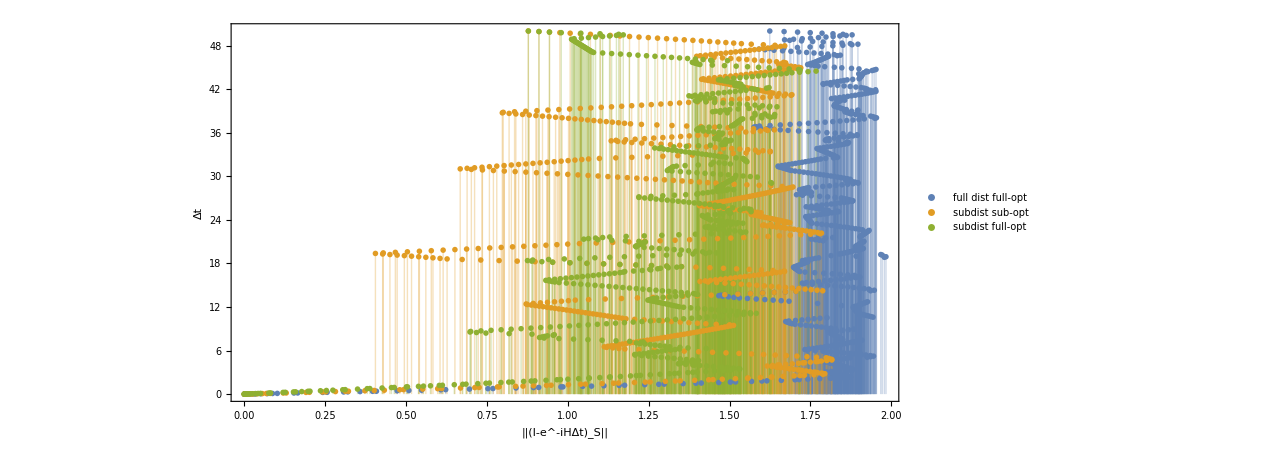

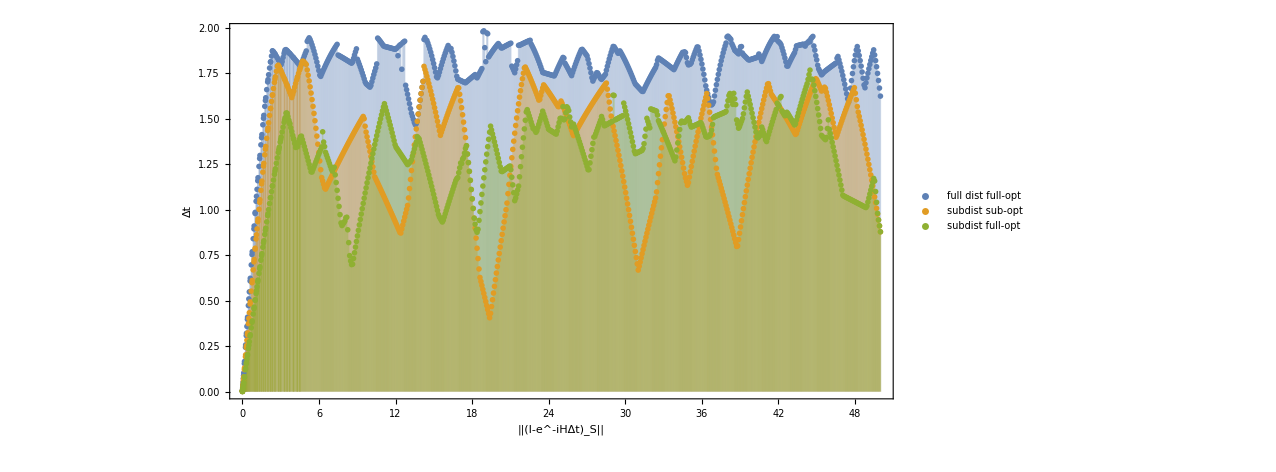

```mathematica
ListPlot[{Transpose@{Values[disttoid][[All,"fullopt"]],Keys@disttoid},Transpose@{Values[disttoid][[All,"subopt"]],Keys@disttoid},Transpose@{Values[disttoid][[All,"fullsubopt"]],Keys@disttoid}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,stylebig[3,{"full dist full-opt","subdist sub-opt","subdist full-opt"},{0.2,0.8}]]

ListPlot[{Transpose@{Keys@disttoid,Values[disttoid][[All,"fullopt"]]},Transpose@{Keys@disttoid,Values[disttoid][[All,"subopt"]]},Transpose@{Keys@disttoid,Values[disttoid][[All,"fullsubopt"]]}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,stylebig[3,{"full dist full-opt","subdist sub-opt","subdist full-opt"},{0.8,0.2}]]
```

DumpSave["distidfull.mx", distidfull];

```mathematica
distid<<distid.mx;
distidfull<<distidfull.mx;
```

```mathematica
Complement[subcompsum//Keys,distid//Keys]
```

{0.007,0.035,0.3,0.35,0.6,0.75,1.1,1.2,1.35,1.65,1.8,2.2,2.35,2.55,2.85,3.3,3.7,4.3}

```mathematica
Keys@distid//Length
{0.007,0.035,0.3,0.35,0.6,0.75,1.1,1.2,1.35,1.65,1.8,2.2,2.35,2.55,2.85,3.3,3.7,4.3}
```

424

{0.007,0.035,0.3,0.35,0.6,0.75,1.1,1.2,1.35,1.65,1.8,2.2,2.35,2.55,2.85,3.3,3.7,4.3}

### Load data

Get best results with distance at least 0.001 (subspace distance) from recompilation

```mathematica
times={0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}
```

{0.001,0.01,0.1,1,4,0.005,0.05,0.5,2,0.002,0.02,0.03,0.07,0.15,0.25,0.3,0.4,0.6,0.75,0.9,1.1,1.2,1.35,1.5,1.65,1.8,2.2,2.35,2.55,2.85,3,3.5,3.3,3.7,4.3,4.5,0.35}

```mathematica
mindist=1*10^-3;
bestsub=<|Table[t->First@MinimalBy[MinimalBy[Select[subcompsum[t],#["distsub"]<=mindist&],Length[#["ansatz"]]&],#["distsub"]&],{t,Keys@subcompsum}]|>;
bestfull=<|Table[t->First@MinimalBy[MinimalBy[Select[fullcompsum[t],#["distsub"]<=mindist&],Length[#["ansatz"]]&],#["distsub"]&],{t,Keys@fullcompsum}]|>;
(*indicate the fail results*)
Print["failed runs on fullspace-compiled for Δt:",Select[bestfull,Length@#===1&]//Keys];
Print["failed runs on subspace-compiled for Δt:",Select[bestsub,Length@#===1&]//Keys];


(*select the successfull results only*)
bestsub=Select[bestsub,Length@#>1&];
bestfull=Select[bestfull,Length@#>1&];
```

First::nofirst: {} has zero length and no first element.

failed runs on fullspace-compiled for Δt:{0.035,0.007}

failed runs on subspace-compiled for Δt:{}

All Trotter results with at distance at most 0.001 (subspace and full-space distances)

```mathematica
tbestsub=<|Table[t->Select[Flatten[Values[trotsumsub[t]],1],#[[2]]<=mindist&],{t,Keys@trotsumsub}]|>;
tbestfull=<|Table[t->Select[Flatten[Values[trotsum[t]],1],#[[2]]<=mindist&],{t,Keys@trotsum}]|>;
```

```mathematica
besttrotsub=<|Table[t->First@MinimalBy[MinimalBy[Select[{Total@#[[1]],#[[2]]}&/@Flatten[Values@trotsumsub[t],1],#[[2]]<=mindist&],#[[1]]&],#[[2]]&],{t,Keys@trotsumsub}]|>;
besttrotfull=<|Table[t->First@MinimalBy[MinimalBy[Select[{Total@#[[1]],#[[2]]}&/@Flatten[Values@trotsum[t],1],#[[2]]<=mindist&],#[[1]]&],#[[2]]&],{t,Keys@trotsum}]|>;
```

Pick the closest distance of trotterization with minimal number of gates
subspace-recompiled vs trotterization with subspace distance

```mathematica
datacompfull=With[{m=Max[Length[#]&/@bestfull⟦All,"ansatz"⟧]},Table[{t,Length@bestfull[t]["ansatz"]},{t,Keys@bestfull}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
datacompsub=With[{m=Max[Length[#]&/@bestsub⟦All,"ansatz"⟧]},Table[{t,Length@bestsub[t]["ansatz"]},{t,Keys@bestsub}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
datatrotsub=With[{m=Max[besttrotsub⟦All,1⟧]},Table[{t,Total@besttrotsub[t][[1]]},{t,Keys@besttrotsub}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
datatrotfull=With[{m=Max[besttrotfull⟦All,1⟧]},Table[{t,Total@besttrotfull[t][[1]]},{t,Keys@besttrotfull}]/.{{d_,m}->Labeled[{d,m},m,Background->None]}]
```

{{0.001,6},{0.01,23},{0.1,28},{1,30},{4,34}34,{0.005,19},{0.05,30},{0.5,28},{2,31},{0.002,13},{0.02,26},{0.03,28},{0.07,26},{0.15,24},{0.25,28},{0.3,23},{0.4,24},{0.6,26},{0.75,25},{0.9,31},{1.1,30},{1.2,30},{1.35,29},{1.5,31},{1.65,29},{1.8,27},{2.2,29},{2.35,26},{2.55,28},{2.85,29},{3,29},{3.5,29},{3.3,33},{3.7,28},{4.3,32},{4.5,33},{0.35,22}}

{{0.001,2},{0.01,14},{0.1,15},{1,16},{4,18}18,{0.005,5},{0.05,12},{0.5,17},{2,16},{0.002,13},{0.035,12},{0.007,16},{0.02,14},{0.03,16},{0.07,17},{0.15,14},{0.25,16},{0.3,14},{0.4,14},{0.6,16},{0.75,16},{0.9,16},{1.1,17},{1.2,15},{1.35,15},{1.5,15},{1.65,17},{1.8,16},{2.2,17},{2.35,17},{2.55,17},{2.85,17},{3,16},{3.5,15},{3.3,18}18,{3.7,18}18,{4.3,17},{4.5,16},{0.35,16}}

{{0.001,78},{0.005,78},{0.01,78},{0.05,78},{0.1,152},{1,468},{2,936},{4,1170}1170,{0.002,78},{0.035,78},{0.007,78},{0.02,78},{0.03,78},{0.07,78},{0.15,152},{0.25,152},{0.5,234},{0.3,234},{0.4,234},{0.6,234},{0.75,386},{0.9,468},{1.1,468},{1.2,468},{1.35,702},{1.5,702},{1.65,702},{1.8,702},{2.2,936},{2.35,936},{2.55,1088},{2.85,1170}1170,{3,1170}1170,{3.5,1170}1170}

{{0.001,78},{0.005,78},{0.01,78},{0.05,78},{0.1,152},{1,468},{2,936},{4,1170}1170,{0.002,78},{0.035,78},{0.007,78},{0.02,78},{0.03,78},{0.07,78},{0.15,152},{0.25,152},{0.5,234},{0.3,234},{0.4,234},{0.6,234},{0.75,386},{0.9,468},{1.1,468},{1.2,468},{1.35,702},{1.5,702},{1.65,702},{1.8,702},{2.2,936},{2.35,936},{2.55,1088},{2.85,1170}1170,{3,1170}1170,{3.5,1170}1170}

### Plot the best results on every methode

```mathematica
rainbowcol[n_]:=Table[ColorData["Rainbow",(i-1)/n],{i,n}]
```

```mathematica
style[ndata_,legends_,legendpos_]:={AspectRatio->2/3,ImageSize->400,
LabelStyle->{FontFamily->"FreeSerif",FontSize->15,Background->None},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,18,FontFamily->"FreeSerif"],
PlotStyle->Reverse@rainbowcol[ndata],PlotMarkers->{Automatic,.02},Background->White,PlotLegends->Placed[PointLegend[Automatic,legends,Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],
legendpos],PlotRange->All,GridLinesStyle->Directive[Black, Dashed]};
```

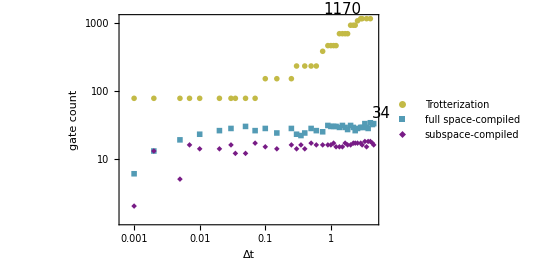

```mathematica
ListLogLogPlot[{datatrotsub,datacompfull,datacompsub},FrameLabel->{"Δt","gate count"},GridLines->{None, {18,34,1170}},style[3,{"Trotterization","full space-compiled","subspace-compiled"},{0.7,0.15}]]
```

```mathematica
hammat=CalcPauliSumMatrix[hamiltonian];subspace={3,5,6,9,10,12};
```

```mathematica
besttrotsub
```

<|0.001→{78,1.431×10^-7},0.005→{78,3.57749×10^-6},0.01→{78,0.0000143099},0.05→{78,0.000357684},0.1→{152,0.0000378907},1→{468,0.000387835},2→{936,0.000536372},4→{1170,0.000785579},0.002→{78,5.72399×10^-7},0.035→{78,0.000175282},0.007→{78,7.01187×10^-6},0.02→{78,0.0000572383},0.03→{78,0.000128781},0.07→{78,0.000700939},0.15→{152,0.000127777},0.25→{152,0.000590029},0.5→{234,0.000210902},0.3→{234,0.0000273976},0.4→{234,0.0000865019},0.6→{234,0.000436583},0.75→{386,0.000787236},0.9→{468,0.000258813},1.1→{468,0.000557176},1.2→{468,0.000772751},1.35→{702,0.000345294},1.5→{702,0.00050238},1.65→{702,0.000697876},1.8→{702,0.000931715},2.2→{936,0.000704111},2.35→{936,0.000835337},2.55→{1088,0.000978671},2.85→{1170,0.000605165},3→{1170,0.000633994},3.5→{1170,0.00059477}|>

```mathematica
datacompsub2=With[{m=Max[Length[#]&/@bestsub⟦All,"ansatz"⟧]},Table[{distidsub[t],Length@bestsub[t]["ansatz"]},{t,times}]];
datatrotsub2=With[{m=Max[besttrotsub⟦All,1⟧]},Table[{distidsub[t],Total@besttrotsub[t]},{t,times}]]
```

{{0.000810213,78.},{0.00162043,78.},{0.00405106,78.},{Missing[KeyAbsent,0.007],78.},{0.00810211,78.},{0.0162041,78.0001},{0.0243058,78.0001},{Missing[KeyAbsent,0.035],78.0002},{0.0405079,78.0004},{0.0567073,78.0007},{0.0809992,152.},{0.121457,152.},{0.202207,152.001},{Missing[KeyAbsent,0.3],234.},{Missing[KeyAbsent,0.35],Total[Missing[KeyAbsent,0.35]]},{0.322669,234.},{0.402342,234.},{Missing[KeyAbsent,0.6],234.},{Missing[KeyAbsent,0.75],386.001},{0.713144,468.},{0.788234,468.},{Missing[KeyAbsent,1.1],468.001},{Missing[KeyAbsent,1.2],468.001},{Missing[KeyAbsent,1.35],702.},{1.1419,702.001},{Missing[KeyAbsent,1.65],702.001},{Missing[KeyAbsent,1.8],702.001},{1.44887,936.001},{Missing[KeyAbsent,2.2],936.001},{Missing[KeyAbsent,2.35],936.001},{Missing[KeyAbsent,2.55],1088.},{Missing[KeyAbsent,2.85],1170.},{1.76596,1170.},{Missing[KeyAbsent,3.3],Total[Missing[KeyAbsent,3.3]]},{1.68374,1170.},{Missing[KeyAbsent,3.7],Total[Missing[KeyAbsent,3.7]]},{1.64856,1170.},{Missing[KeyAbsent,4.3],Total[Missing[KeyAbsent,4.3]]},{1.81781,Total[Missing[KeyAbsent,4.5]]}}

```mathematica
ListPlot[
{datatrotsub2,datacompsub2},GridLines->None,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","subspace compilation","subspace compilation"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.25,0.8}],FrameLabel->{"distance to id matrix","gate count"},ImageSize->Large,PlotMarkers->"OpenMarkers",style]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Function::slot: Slot[«1»] (in Framed[Slot[«1»],Rule[«2»],Rule[«2»]]&) should contain a non-negative integer or string.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

ListPlot::nonopt: Options expected (instead of style) beyond position 1 in ListPlot[{{{0.000810213,78.},{0.00810211,78.},{0.0809992,152.},{0.788234,468.},{1.64856,1170.},{0.00405106,78.},{0.0405079,78.0004},{0.402342,234.},{1.44887,936.001},{0.00162043,78.},«27»},{{0.000810213,2},{0.00810211,14},{0.0809992,15},{0.788234,16},{1.64856,18},{«22»,5},{0.0405079,12},{0.402342,17},{1.44887,16},{0.00162043,13},«27»}},«5»,style]. An option must be a rule or a list of rules.

ListPlot[{{{0.000810213,78.},{0.00810211,78.},{0.0809992,152.},{0.788234,468.},{1.64856,1170.},{0.00405106,78.},{0.0405079,78.0004},{0.402342,234.},{1.44887,936.001},{0.00162043,78.},{0.0162041,78.0001},{0.0243058,78.0001},{0.0567073,78.0007},{0.121457,152.},{0.202207,152.001},{Missing[KeyAbsent,0.3],234.},{0.322669,234.},{Missing[KeyAbsent,0.6],234.},{Missing[KeyAbsent,0.75],386.001},{0.713144,468.},{Missing[KeyAbsent,1.1],468.001},{Missing[KeyAbsent,1.2],468.001},{Missing[KeyAbsent,1.35],702.},{1.1419,702.001},{Missing[KeyAbsent,1.65],702.001},{Missing[KeyAbsent,1.8],702.001},{Missing[KeyAbsent,2.2],936.001},{Missing[KeyAbsent,2.35],936.001},{Missing[KeyAbsent,2.55],1088.},{Missing[KeyAbsent,2.85],1170.},{1.76596,1170.},{1.68374,1170.},{Missing[KeyAbsent,3.3],Total[Missing[KeyAbsent,3.3]]},{Missing[KeyAbsent,3.7],Total[Missing[KeyAbsent,3.7]]},{Missing[KeyAbsent,4.3],Total[Missing[KeyAbsent,4.3]]},{1.81781,Total[Missing[KeyAbsent,4.5]]},{Missing[KeyAbsent,0.35],Total[Missing[KeyAbsent,0.35]]}},{{0.000810213,2},{0.00810211,14},{0.0809992,15},{0.788234,16},{1.64856,18},{0.00405106,5},{0.0405079,12},{0.402342,17},{1.44887,16},{0.00162043,13},{{0.0162041,0.00654141},14},{{0.0243058,0.00981212},16},{0.0567073,17},{0.121457,14},{0.202207,16},{Missing[KeyAbsent,0.3],14},{0.322669,14},{Missing[KeyAbsent,0.6],16},{Missing[KeyAbsent,0.75],16},{0.713144,16},{Missing[KeyAbsent,1.1],17},{Missing[KeyAbsent,1.2],15},{Missing[KeyAbsent,1.35],15},{1.1419,15},{Missing[KeyAbsent,1.65],17},{Missing[KeyAbsent,1.8],16},{Missing[KeyAbsent,2.2],17},{Missing[KeyAbsent,2.35],17},{Missing[KeyAbsent,2.55],17},{Missing[KeyAbsent,2.85],17},{1.76596,16},{1.68374,15},{Missing[KeyAbsent,3.3],18},{Missing[KeyAbsent,3.7],18},{Missing[KeyAbsent,4.3],17},{1.81781,16},{Missing[KeyAbsent,0.35],16}}},GridLines→None,PlotLegends→Placed[PointLegend[Automatic,{Trotterization,subspace compilation,subspace compilation},Spacings→0.,LegendFunction→(#1&)],{0.25,0.8}],FrameLabel→{distance to id matrix,gate count},ImageSize→Large,PlotMarkers→OpenMarkers,style]

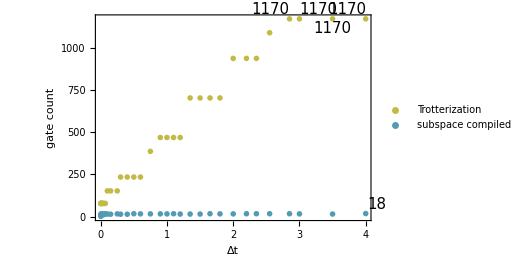

```mathematica
ListPlot[
{datatrotsub,datacompsub},GridLines->None,PlotLegends->Placed[PointLegend[Automatic,{"Trotterization","subspace compiled"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.25,0.8}],FrameLabel->{"Δt","gate count"},ImageSize->Large,PlotMarkers->"OpenMarkers",style]
```

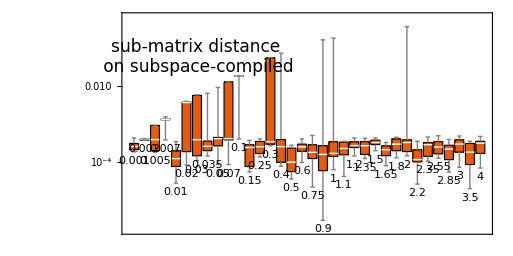

```mathematica
BoxWhiskerChart[Table[subcompsum[t][[All,"distsub"]],{t,times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["sub-matrix distance\n on subspace-compiled",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.8}]],ImageSize->400,AspectRatio->1/2,
ImagePadding->{{50,10},{37,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.5], Directive[Red,Thick ,Dashed]},ImageSize->Large
]
```

### Trotterizations

```mathematica
stylebig[n_,legends_,legendpos_]:={AspectRatio->1/2,ImageSize->600,
LabelStyle->{FontFamily->"FreeSerif",FontSize->18,Background->None},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Black,19,FontFamily->"FreeSerif"],
PlotMarkers->"OpenMarkers",Background->White,PlotLegends->Placed[PointLegend[Automatic,legends,Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],
legendpos],PlotRange->All,GridLinesStyle->Directive[Black, Dashed]};
```

```mathematica
distidfull<<distidfull.mx;
distidsub<<distidsub.mx;
```

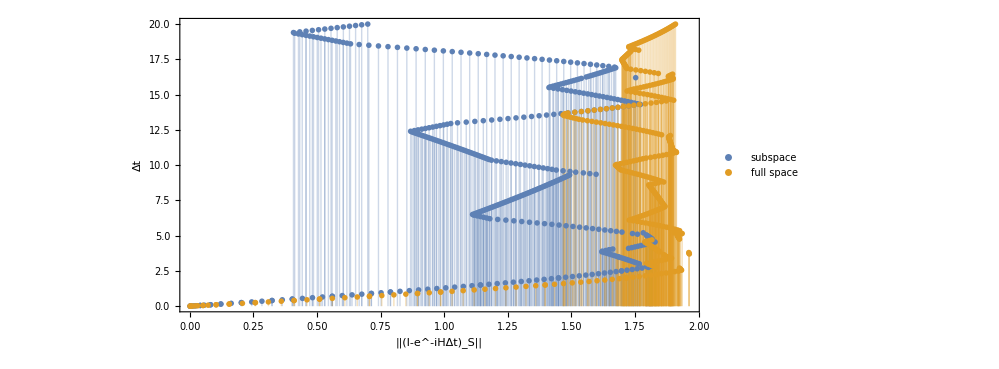

```mathematica
ListPlot[{Transpose@{Values@distidsub,Keys@distidsub},Transpose@{Values@distidfull,Keys@distidfull}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,stylebig[2,{"subspace","full space"},{0.12,0.7}]]
```

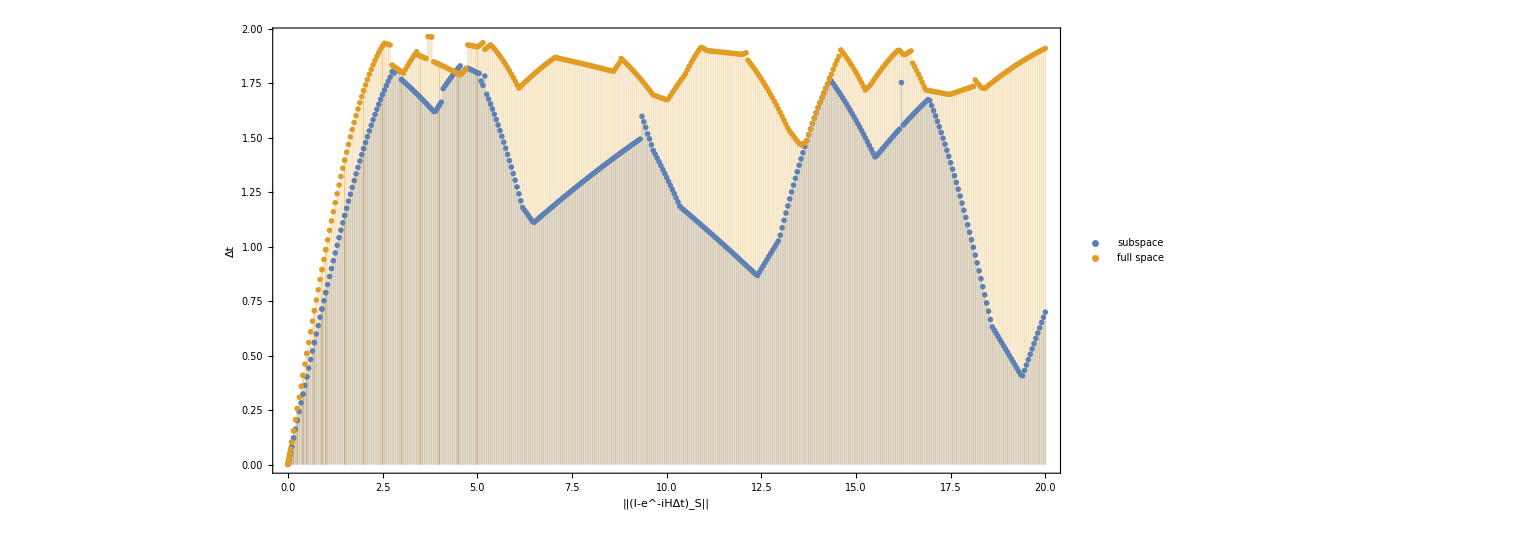

```mathematica
ListPlot[{Transpose@{Keys@distidsub,Values@distidsub},Transpose@{Keys@distidfull,Values@distidfull}},FrameLabel->{TraditionalForm["||(I-e^-iHΔt)_S||"],"Δt"},Filling->Bottom,stylebig[2,{"subspace","full space"},{0.12,0.7}]]
```

### Recompilation results

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/dynamics

```mathematica
times=Sort@Keys@subcompsum
```

{0.001,0.002,0.005,0.007,0.01,0.02,0.03,0.035,0.05,0.07,0.1,0.15,0.25,0.5,1,2,4}

```mathematica
data=Table[RandomVariate[NormalDistribution[μ,1],10],{μ,{0,3,2,5}},{2}]
```

{{{-0.62805,0.503139,-0.494432,1.3825,0.806005,-1.20586,-1.6322,0.270215,0.57163,-0.858467},{-0.398531,1.46245,0.522917,-0.0665072,-0.269048,0.94427,0.114433,-0.0530903,-0.204544,-0.051371}},{{2.65654,3.20133,2.757,2.5076,3.65194,3.32971,4.1456,1.92531,1.55744,2.69508},{4.4198,1.77036,3.63616,3.56958,4.2051,1.92865,2.51282,1.54148,3.14746,4.16609}},{{3.69844,2.63426,1.45459,2.63781,1.111,1.73925,1.18212,0.801854,3.00952,3.54192},{2.57924,0.327004,1.93919,2.68027,2.03904,3.06969,1.63642,0.950428,3.54201,1.03972}},{{5.19373,5.32771,3.86425,4.31977,5.74075,6.46626,3.85115,5.14925,6.67209,5.87086},{5.28371,5.33527,5.3631,5.41208,4.69648,6.21761,4.94647,4.85357,4.07642,4.41286}}}

```mathematica
subcompsum[1][[1]]
```

<|cost→2.23578×10^-9,distfull→1.7243,distsub→0.0000615311,ansatz→{Rz_0[-3.0801],C_1[Rz_3[-8.73735]],C_3[Ry_1[3.14159]],C_2[Rz_1[-8.3749]],C_1[Rz_3[-9.32908]],C_2[Ry_0[3.14154]],C_2[Rx_3[3.14159]],C_3[Rx_1[-3.14159]],C_3[Ry_2[-0.362331]],C_0[Rx_2[8.97569]],C_1[Ry_2[0.362319]],C_0[Rx_2[-8.96725]],C_2[Rz_3[-3.18653]],C_2[Ry_0[-3.14163]],C_2[Ry_3[3.14159]],C_1[Rz_2[-11.7368]],C_2[Ry_1[3.14159]]},runtime→2.34237|>

```mathematica
color
```

{RGBColor[0.7285450767713475, 0.03494508851712408, 0.14198068147566834],RGBColor[0.4582847199296809, 0.6086754253762674, 0.6585971050832811]}

```mathematica
Around@subcompsum[0.1][[All,"distsub"]]
```

0.0150.008

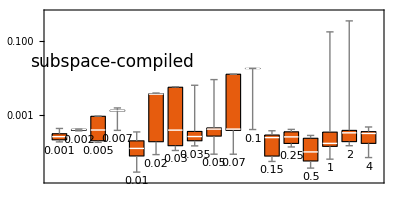

```mathematica
BoxWhiskerChart[Table[subcompsum[t][[All,"distsub"]],{t,times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], Automatic],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["subspace-compiled",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.7}]],ImageSize->400,AspectRatio->1/2,
ImagePadding->{{50,10},{37,10}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]}
]
```

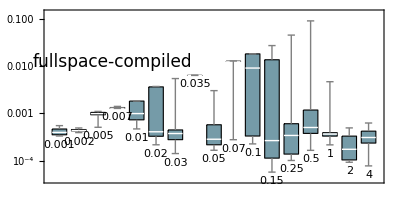

```mathematica
BoxWhiskerChart[Table[fullcompsum[t][[All,"distsub"]],{t,times}],ScalingFunctions->"Log2",FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->Directive[EdgeForm[Black], color[[2]]],ChartLabels->Placed[times,Below],PlotTheme->"Scientific",Epilog->Text[Style["fullspace-compiled",17,FontFamily->"FreeSerif",Background->White],Scaled[{.2,.7}]],ImageSize->400,ImagePadding->{{50,10},{37,0}},GridLines->{Range[Length@times],{Log2@(10^-3)}},GridLinesStyle->{GrayLevel[0.1,0.3], Directive[Red,Thick ,Dashed]},AspectRatio->1/2
]
```

```mathematica
Directory[]
```

/home/cica/postox/papers/chemistry-code/vqe

```mathematica
subcompsum
```

<|0.001→{<|cost→9.55291×10^-8,distfull→0.232902,distsub→0.00037415,ansatz→{Rx_3[0.00154887],C_2[Rz_3[-0.232746]],Rx_3[-0.00155846],C_0[Rz_3[0.233532]],C_3[Rz_1[0.233399]],C_1[Rz_2[0.000497306]],C_0[Rz_1[0.466841]],Rz_1[-0.350486]},runtime→0.39558|>,8,<|cost→4.99707×10^-8,distfull→0.00123118,distsub→0.000299726,ansatz→{C_1[Rz_3[0.00117034]],C_0[Rz_2[-0.00117723]],Rz_2[0.0015176]},runtime→0.26575|>},0.002→{1},13,2→{<|cost→8.82211×10^-8,3,runtime→2.75748|>,8,<|1|>},4→{1}|>
 |  |  |  |

```mathematica
succompsub=<|Table[t->Select[subcompsum[t],#["distsub"]<=mindist&],{t,Keys@subcompsum}]|>;
succompfull=<|Table[t->Select[fullcompsum[t],#["distsub"]<=mindist&],{t,Keys@fullcompsum}]|>;
```

```mathematica
data
```

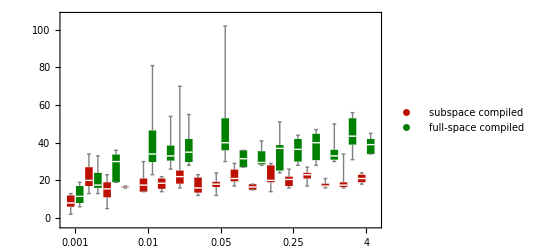

```mathematica
BoxWhiskerChart[Transpose@{Table[Length@#&/@succompsub[t][[All,"ansatz"]],{t,times}],Table[Length@#&/@succompfull[t][[All,"ansatz"]],{t,times}]},FrameStyle->Directive[Black,16,FontFamily->"FreeSerif"],Background->White,ChartStyle->58,ChartLabels->{Placed[times,Axis,Rotate[#,45Degree]&],None},ImageSize->600,ChartLegends->Placed[PointLegend[Automatic,{"subspace compiled","full-space compiled"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.15,0.88}]]
```

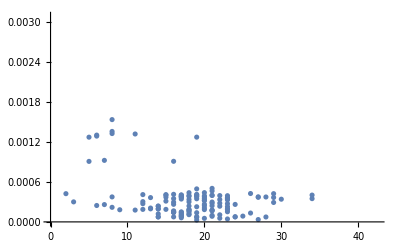

```mathematica
ListPlot[{#[[3]],#[[2]]}&/@Flatten[Values[ressubH2],1]]
```

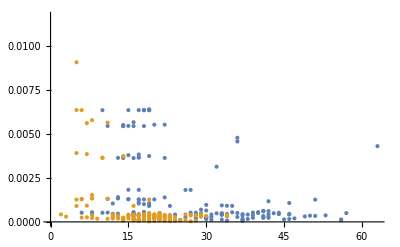

```mathematica
ListPlot[{{#[[3]],#[[2]]}&/@Flatten[Values[resfullH2],1],{#[[3]],#[[2]]}&/@Flatten[Values[ressubH2],1]}]
```